```mathematica
CoordinateTable = {{0.23, 5.38}, {0.31, 5.32}, {0.40, 5.23}, {0.48, 5.14}, {0.56, 5.04}, {0.67, 4.99}, {0.75, 4.85}, {0.86, 4.76}, {0.96, 4.62}, {1.05, 4.49}, {1.18, 4.40}, {1.32, 4.26}, {1.48, 4.10}, {1.64, 3.92}, {1.84, 3.76}, {2.15, 3.5}}
```

{{0.23,5.38},{0.31,5.32},{0.4,5.23},{0.48,5.14},{0.56,5.04},{0.67,4.99},{0.75,4.85},{0.86,4.76},{0.96,4.62},{1.05,4.49},{1.18,4.4},{1.32,4.26},{1.48,4.1},{1.64,3.92},{1.84,3.76},{2.15,3.5}}

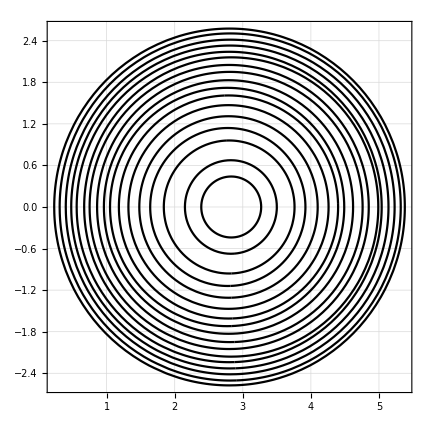

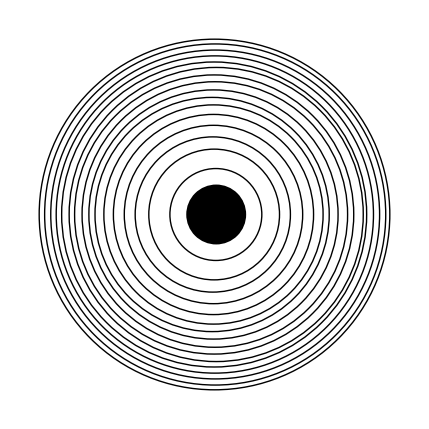

```mathematica
DrawRing[x1_,x2_]:=ContourPlot[(x-((x2-x1)/2+x1))^2+(y)^2==((x2-x1)/2)^2,{x,x1,x2},{y,-(x2-x1)/2,(x2-x1)/2},GridLines->Automatic, PlotTheme->"Monochrome"];
Show[DrawRing[2.39,3.27],Table[DrawRing[CoordinateTable[[i,1]],CoordinateTable[[i,2]]],{i,1,Length[CoordinateTable]}],PlotRange->All]
Show[Graphics[Disk[{(3.27-2.39)/2+2.39,0},(3.27-2.39)/2]],Table[Graphics[
Circle[{CoordinateTable[[i,1]]+(CoordinateTable[[i,2]]-CoordinateTable[[i,1]])/2,0},(CoordinateTable[[i,2]]-CoordinateTable[[i,1]])/2]
],{i,1,Length[CoordinateTable]}]]
```

Цена деления:

```mathematica
c=1/100*9
```

9/100

Погрешность цены деления:

```mathematica
Sqrt[D[a*b/100,b]^2*0.5^2]
```

0.005 √(a^2)

{{1,0.747225,0.0238578},{2,1.39134,0.0427375},{3,2.1009,0.0524031},{4,2.71391,0.0595024},{5,3.40475,0.0500653},{6,4.06498,0.0546612},{7,4.72428,0.0297652},{8,5.37131,0.0523829}}

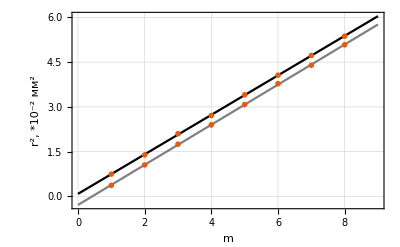

\left(
\begin{array}{ccccc}
 1 & 0.747225 & 0.0238578 & 0.369077 & 0.00569854 \\
 2 & 1.39134 & 0.0427375 & 1.0547 & 0.0464399 \\
 3 & 2.1009 & 0.0524031 & 1.75163 & 0.0478897 \\
 4 & 2.71391 & 0.0595024 & 2.39922 & 0.0837414 \\
 5 & 3.40475 & 0.0500653 & 3.08035 & 0.0319832 \\
 6 & 4.06498 & 0.0546612 & 3.77914 & 0.005 \\
 7 & 4.72428 & 0.0297652 & 4.39773 & 0.0380757 \\
 8 & 5.37131 & 0.0523829 & 5.08295 & 0.0308437 \\
\end{array}
\right)

```mathematica
PointCenter = (3.27-2.39)/2+2.39;
CoordinateTable2=CoordinateTable;
ClearAll[i];
MeanError[x_]:=√(1/(Length[x]*(Length[x]-1))Sum[(x[[i]]-Mean[x])^2,{i,1,Length[x]}]);
Dark =Table[0,{i,8},{j,2}];
Light =Table[0,{i,8},{j,2}];
For[i=1,i≤Length[CoordinateTable2],i++,
CoordinateTable2[[i,1]]=((CoordinateTable2[[i,1]]-PointCenter)*c)^2*100;
CoordinateTable2[[i,2]]=((CoordinateTable2[[i,2]]-PointCenter)*c)^2*100;
]
For[i=1,i<=15,i=i+2,
Dark[[(Floor[i/2]+1),1]]=CoordinateTable2[[i,1]];
Dark[[(Floor[i/2]+1),2]]=CoordinateTable2[[i,2]];
Light[[(Floor[i/2]+1),1]]=CoordinateTable2[[i+1,1]];
Light[[(Floor[i/2]+1),2]]=CoordinateTable2[[i+1,2]];
]
TotalError[x1_,x2_,xc_,a_]:=N[Sqrt[(a^2 (x1-xc))^2*0.005^2+(a^2 (x2-xc))^2*0.005^2+(1/2 (-2 a^2 (x1-xc)-2 a^2 (x2-xc)))^2*0.005^2+(1/4 (2 a (x1-xc)^2+2 a (x2-xc)^2)^2)*0.05^2],3]
For[i = 1,i≤8, i++,
Dark[[i,1]]=Mean[{Dark[[i,1]],Dark[[i,2]]}];
Dark[[i,2]]=Sqrt[MeanError[{Dark[[i,1]],Dark[[i,2]]}]^2+0.005^2];
Light[[i,1]]=Mean[{Light[[i,1]],Light[[i,2]]}];
Light[[i,2]]=Sqrt[MeanError[{Light[[i,1]],Light[[i,2]]}]^2+0.005^2];
]
Summed=Table[0,{i,8},{j,5}];
For[i=1,i≤8,i++,
Summed[[i,1]]=9-i;
Summed[[i,2]]=Dark[[i,1]];
Summed[[i,3]]=Dark[[i,2]];
Summed[[i,4]]=Light[[i,1]];
Summed[[i,5]]=Light[[i,2]];
]
Summed=Reverse[Summed];
TeXForm[Summed]
Needs["ErrorBarPlots`"];
ApproxLineDark = LinearModelFit[Summed[[1;;8,1;;2]],x,x];
Dark=Summed[[1;;8,1;;3]]
For[i=1,i<=8,i++,
Dark[[i,3]]=ErrorBar[0,Dark[[i,3]]];
]
DarkGraph=Partition[Riffle[Dark[[1;;8,1;;2]],Dark[[1;;8,3]]],2];
Light=Table[0,{i,8},{j,3}];
For[i=1,i≤8,i++,
Light[[i,1]]=i;
Light[[i,2]]=Summed[[i,4]];
Light[[i,3]]=ErrorBar[Summed[[i,5]]];
]
ApproxLineLight=LinearModelFit[Light[[1;;8,1;;2]],x,x];
LightGraph=Partition[Riffle[Light[[1;;8,1;;2]],Light[[1;;8,3]]],2];
Show[Plot[ApproxLineDark[x],{x,0,9}, PlotTheme->"Scientific",PlotStyle->Black],Plot[ApproxLineLight[x],{x,0,9}, PlotTheme->"Scientific",PlotStyle->Gray],ErrorListPlot[DarkGraph, PlotTheme->"Scientific",PlotStyle->AbsolutePointSize[4]],ErrorListPlot[LightGraph, PlotTheme->"Scientific",PlotStyle->AbsolutePointSize[4]],PlotRange->All, GridLines->Automatic,FrameLabel->{{RawBoxes[RowBox[{SuperscriptBox["r","2"],","," ",RowBox[{"*",SuperscriptBox["10","-2"]," ",SuperscriptBox["мм","2"]}]}]],None},{HoldForm[m],None}},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
ApproxLineDark["ParameterTable"]
ApproxLineLight["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.0853841 | 0.0136641 | 6.24878 | 0.000778545
x | 0.662101 | 0.0027059 | 244.688 | 3.14424×10^-13

| Estimate | Standard Error | t-Statistic | P-Value
1 | -0.286148 | 0.0154278 | -18.5476 | 1.58439×10^-6
x | 0.672333 | 0.00305516 | 220.065 | 5.94101×10^-13

WolframAlphaQueryParseResults

5/91 mm

0.662*10^(-2) mm^2/546 nm in meters

WolframAlphaQueryResults

```mathematica
Sqrt[D[(x*10^-2)/(546*10^-6),x]^2*0.003^2]
```

0.0549451

```mathematica
Solve[rm==√(((2m-1)R λ)/2),R]
```

{{R→(2 rm^2)/((-1+2 m) λ)}}

0.672

```mathematica
(2 rm^2)/((-1+2 m) λ)/(rm^2/m)
```

(2 m)/((-1+2 m) λ)

```mathematica
Quantity[0.00672,("Millimeters")^2]/Quantity[546,"Nanometers"]
```

12.3077 mm

```mathematica
Rw=Quantity[0.00672,("Millimeters")^2]/Quantity[546,"Nanometers"]
```

12.3077 mm

```mathematica
Rb=Quantity[0.00662,("Millimeters")^2]/Quantity[546,"Nanometers"]
```

12.1245 mm

```mathematica
Mean[{Rw,Rb}]
```

12.2161 mm

```mathematica
Sqrt[MeanError[{Rw,Rb}]^2+Quantity[0.05,"Millimeters"]^2]
```

0.104336 mm